# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["C:\\Users\\Miguel\\Github\\Entropy\\Prethermalization\\Survival and entanglement\\QMB.wl"];
```

MessageName::messg: TranslationEigenvectorRepresentatives::usage cannot be set to FormatUsage[TranslationEigenvectorRepresentatives[L] returns a list of sublists, each containing:  the decimal representation of a bit-string representative eigenvector,  its pseudomomentum k, and the length of its translation orbit,  for a system of ```L``` qubits.]. It must be set to a string.

MessageName::messg: BlockDiagonalize::usage cannot be set to FormatUsage[BlockDiagonalize[matrix,opts] returns ```matrix``` in block-diagonal form. Only 	option is '''Symmetry'''.]. It must be set to a string.

MessageName::messg: Symmetry::usage cannot be set to FormatUsage[Symmetry is an option for '''BlockDiagonalize''' to specify the symmetry according to which 	```matrix``` in '''BlockDiagonalize'''[```matrix```] is block diagonalized. It takes the values: 	"Translation". Default option is "Translation".]. It must be set to a string.

General::stop: Further output of MessageName::messg will be suppressed during this calculation.

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[0,1]]+I RandomVariate[NormalDistribution[0,1]],{2^L}]];
(*haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[0,1]],{2^L}]];*)
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
cp=ResourceFunction["CombinePlots"];
```

```mathematica
Clear[rhoa];
rhoa[ini_,t_,L_,k_,val_,vec_]:=Module[{M,rhoc,rhob,rho,ck=Conjugate[vec] . ini,phases=arrayt[t,val,vec],perm=Delete[Range[L],{k}]},
MatrixPartialTrace[Dyad[N[Total[phases*ck]]],perm,2]
];
(*Clear[new];
new[ini_,t_,L_,k_,val_,vec_]:=Module[{ope=Pauli[3],rho=rhoa[ini,t,L,k,val,vec]},
Total[Map[VNentropy,(Chop[Eigenvalues[rho]])]]
];*)
Clear[sdiagonal];
sdiagonal[ini_,L_,k_]:=Module[{rho=Dyad[ini],perm=Delete[Range[L],{k}],rhoa},
rhoa=MatrixPartialTrace[Dyad[ini],perm,2];
Total[Map[VNentropy,(Chop[Eigenvalues[rhoa]])]]
];
```

```mathematica
Clear[rhoa];
rhoa[ini_,t_,L_,k_,val_,vec_]:=Module[{M,rhoc,rhob,rho,ck=Conjugate[vec] . ini,phases=arrayt[t,val,vec],perm=Delete[Range[L],{k}]},
MatrixPartialTrace[Dyad[N[Total[phases*ck]]],perm,2]
];
Clear[mag];
mag[L_,k_,ini_,t_,val_,vec_]:=Module[{ope=Pauli[3],rho=rhoa[ini,t,L,k,val,vec]},
Chop[Tr[rho.ope]]
];
Clear[vnentropy];
vnentropy[L_,k_,ini_,t_,val_,vec_]:=Module[{rho=rhoa[ini,t,L,k,val,vec]},
Total[Map[VNentropy,(Chop[Eigenvalues[rho]])]]
];
Clear[ClusterByWindow];
ClusterByWindow[energies_List,window_]:=Module[{e,s=Sort[energies],clusters={},curr,mn,mx},If[s==={},Return[{}]];
curr={First[s]};mn=mx=First[s];
Do[e=x;
If[Max[mx,e]-Min[mn,e]<=window,AppendTo[curr,e];mn=Min[mn,e];mx=Max[mx,e],AppendTo[clusters,curr];curr={e};mn=mx=e],{x,Rest[s]}];
AppendTo[clusters,curr];
clusters];
```

```mathematica
Clear[arrayt];
arrayt[t_,val_,vec_]:=Exp[-I*val*t]*vec;
```

```mathematica
Clear[new];
new[L_,eigenval_,eigenvec_,ini_,t_]:=Module[{schmidt,psit,ck=Conjugate[eigenvec].ini,d=2^(L/2),phases=arrayt[t,eigenval,eigenvec]},psit=ArrayReshape[N[Total[ck*phases]],{d,d}];
Total[Map[VNentropy,(Chop[SingularValueList[psit]])^2]]];
Clear[sur];
sur[eigenval_,eigenvec_,ini_,t_]:=Module[{psit,phases=arrayt[t,eigenval,eigenvec],ck=Conjugate[eigenvec].ini},
Abs[Conjugate[N[Total[ck*phases]]].ini]^2
];
```

# Svn

```mathematica
J=1;
g=1;
tlist=Table[10^i,{i,-1,10,0.0025}];
tlist//Length
```

4401

```mathematica
hlist=Table[10^i,{i,-6,-1,0.25}];
hlist=Sort[AppendTo[hlist,0.0]];
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
hlist//Length
```

22

```mathematica
L=8;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
productstatesfull=Table[RandomChainProductState[L],10];
```

```mathematica
allvalues={};
allvectors={};

Do[

H=IsingNNOpenHamiltonian[1,hlist[[h]],J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];

AppendTo[allvalues,allvals];
AppendTo[allvectors,allvecs];

,{h,Length[hlist]}];
```

```mathematica
allplots={};
Do[

(*HALF ENTROPY*)
entropy=ParallelTable[new[L,allvalues[[h]],allvectors[[h]],j,t],{j,productstatesfull},{t,tlist},DistributedContexts->Full];
(*Export["SRN_entropy_g_1_hlist_"<>ToString[h]<>".m",entropy];*)
(*time=ParallelTable[sur[allvalues[[h]],allvectors[[h]],j,t],{j,productstatesfull},{t,tlist},DistributedContexts->Full];*)
(*Export["SRN_survival_g_1_hlist_"<>ToString[h]<>".m",time];*)

plots=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[entropy]}],MovingAverage[Transpose[{tlist,Mean[entropy]}],200]},PlotStyle->{Directive[Gray,Opacity[0.10]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}],LogLinearPlot[{pageEntropy[1,7],pageEntropy[4,4]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Gray,Dashed],Directive[Orange,Dashed],Directive[Brown,Dashed],Directive[Purple,Dashed],Directive[Blue,Dashed],Directive[Blue,Dashed]}]},PlotRange->{All,{0,pageEntropy[4,4]}}];

(*plots=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[entropy]}],MovingAverage[Transpose[{tlist,Mean[entropy]}],200]},PlotStyle->{Directive[Gray,Opacity[0.10]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = 1, h = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}],LogLinearPlot[{pageEntropy[1,7],pageEntropy[4,4]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Gray,Dashed],Directive[Orange,Dashed],Directive[Brown,Dashed],Directive[Purple,Dashed],Directive[Blue,Dashed],Directive[Blue,Dashed]}]},PlotRange->{All,{0,pageEntropy[4,4]}}];*)

AppendTo[allplots,plots];

,{h,Length[hlist]}];
```

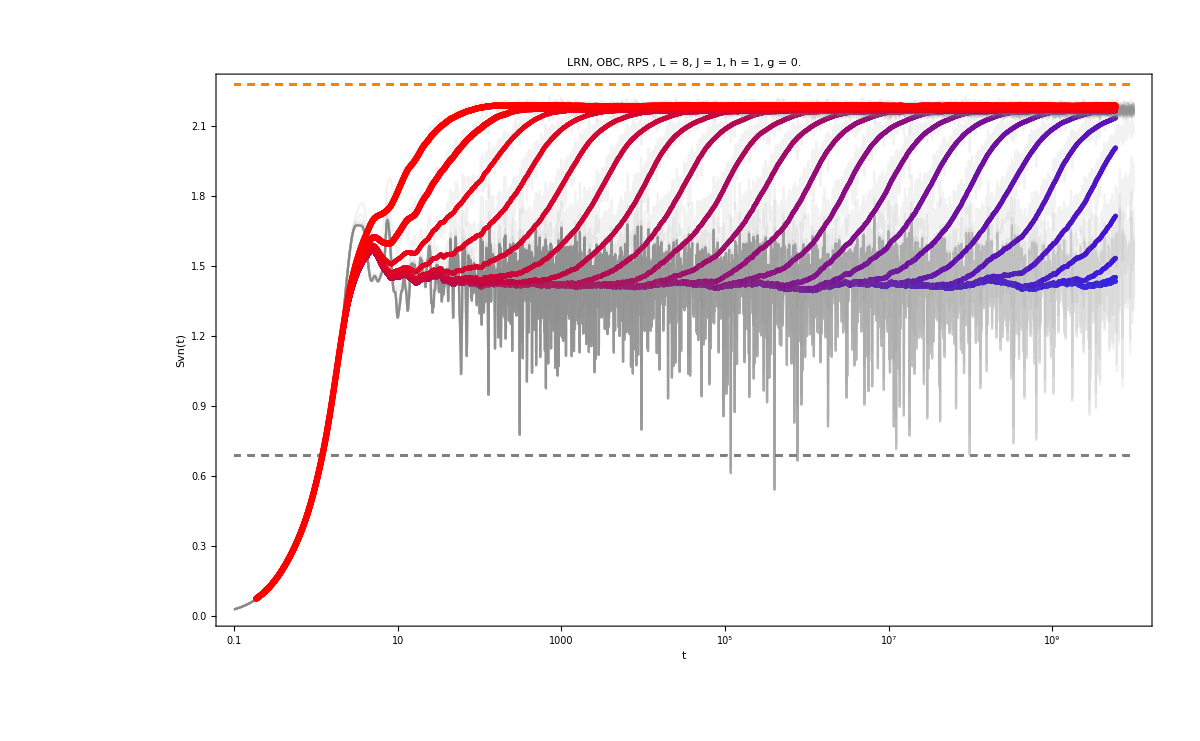

```mathematica
Show[allplots]
```

## Method

```mathematica
allvalues={};
allvectors={};

Do[

H=IsingNNOpenHamiltonian[1,hlist[[h]],J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];

AppendTo[allvalues,allvals];
AppendTo[allvectors,allvecs];

,{h,Length[hlist]}];
```

```mathematica
allplots={};
Do[

(*HALF ENTROPY*)
(*entropy=ParallelTable[new[L,allvalues[[h]],allvectors[[h]],j,t],{j,productstatesfull},{t,tlist},DistributedContexts->Full];
Export["LRN_entropy_h_1_glist_"<>ToString[h]<>".m",entropy];
time=ParallelTable[sur[allvalues[[h]],allvectors[[h]],j,t],{j,productstatesfull},{t,tlist},DistributedContexts->Full];
Export["LRN_survival_h_1_glist_"<>ToString[h]<>".m",time];*)

entropy=Import["/Users/pcs/Desktop/Entropy/schmidt modes/Observables prethermalization/LRN_entropy_h_1_glist_"<>ToString[h]<>".m"];

plots=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[entropy]}],MovingAverage[Transpose[{tlist,Mean[entropy]}],200]},PlotStyle->{Directive[Gray,Opacity[0.10]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}],LogLinearPlot[{pageEntropy[1,9],pageEntropy[5,5]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Gray,Dashed],Directive[Orange,Dashed],Directive[Brown,Dashed],Directive[Purple,Dashed],Directive[Blue,Dashed],Directive[Blue,Dashed]}]},PlotRange->{All,{0,pageEntropy[5,5]}}];

AppendTo[allplots,plots];

,{h,Length[hlist]}];
```

# Survival

```mathematica
ipr=Table[Total[Abs[Conjugate[allvectors[[1]]].j]^4],{j,productstatesfull}];
```

```mathematica
plots={};
Do[

time=ParallelTable[sur[allvalues[[h]],allvectors[[h]],j,t],{j,productstatesfull},{t,tlist},DistributedContexts->Full];
(*time=Import["/Users/pcs/Desktop/Entropy/schmidt modes/Observables prethermalization/LRN_survival_h_1_glist_"<>ToString[h]<>".m"];*)
(*ipr=Table[Total[Abs[Conjugate[allvectors[[h]]].j]^4],{j,productstatesfull}];*)

(*plot1=Table[Show[{ListLogLogPlot[{Transpose[{tlist,time[[i]]}],MovingAverage[Transpose[{tlist,time[[i]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.5]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-4,1}},Joined->{True,False},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["OBC, L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],LogLogPlot[ipr[[i]],{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Dashed],Directive[Red,Dashed]}]}],{i,Length[productstatesfull]}];*)

plot1=Show[{ListLogLogPlot[{Transpose[{tlist,Mean[time]}],MovingAverage[Transpose[{tlist,Mean[time]}],200]},PlotStyle->{Directive[Gray,Opacity[0.5]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-4,1}},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],LogLogPlot[Mean[ipr],{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Dashed],Directive[Red,Dashed]}]}];

(*plot1=Show[{ListLogLogPlot[{Transpose[{tlist,Mean[time]}],MovingAverage[Transpose[{tlist,Mean[time]}],200]},PlotStyle->{Directive[Gray,Opacity[0.5]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-4,1}},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, RPS L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = 1, h = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],LogLogPlot[Mean[ipr],{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Dashed],Directive[Red,Dashed]}]}];*)


AppendTo[plots,Show[plot1]];
(*AppendTo[iprs,{hlist[[h]],ipr}];*)

,{h,Length[hlist]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

# Sp & SVN

```mathematica
{hx,hz,J,L}={-0.01,-1,-1,8};
```

```mathematica
Ha=-IsingHamiltonian[hx, hz, J, L,BoundaryConditions->"Periodic"];
```

```mathematica
system=BlockDiagonalize[Ha, Symmetry->"Translation"];
```

```mathematica
P=Transform[Ha,Symmetry->"Translation"];
```

```mathematica
{eigenvalb,eigenvecb}=Transpose[Sort[Transpose[Eigensystem[system]]]];
```

```mathematica
neweigenvecs=ParallelTable[Transpose[P].i,{i,eigenvecb}];
```

```mathematica
tlist=Table[10^i,{i,-1,6,0.0025}];
tlist//Length
```

2801

```mathematica
productstatesfull=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],{i,2}];
```

```mathematica
entropydata=ParallelTable[{t,new[j,t,L/2,eigenvalb,neweigenvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
```

```mathematica
entropyplotb=Show[{ListLogLinearPlot[{Mean[entropydata],MovingAverage[Mean[entropydata],100]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]]<>", Half Haar states ",35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic,PlotStyle->Directive[Red,PointSize[0.004]]],LogLinearPlot[pageEntropy[L/2,L/2],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->All]
```